```mathematica
Match1=Map[Style[#,Green]&,{Caroline<->Kato,Caroline<->Xari,Dieuw<->Kaat,Dieuw<->Sofia,Kaat<->Sofia,Kato<->Xari}]
```

{Caroline<->Kato,Caroline<->Xari,Dieuw<->Kaat,Dieuw<->Sofia,Kaat<->Sofia,Kato<->Xari}

```mathematica
Match2=Map[Style[#,Red]&,{Caroline<->Kaat,Caroline<->Kaat,Caroline<->Louise,Kaat<->Louise,Dieuw<->Kato,Xari<->Kato,Xari<->Dieuw,Xari<->Dieuw}];
```

```mathematica
Match3=Map[Style[#,Blue]&,{Xari<->Elise,Xari<->Kaat,Kaat<->Elise,Caroline<->Kato,Caroline<->Dieuw,Kato<->Dieuw}]
```

{Xari<->Elise,Xari<->Kaat,Kaat<->Elise,Caroline<->Kato,Caroline<->Dieuw,Kato<->Dieuw}

```mathematica
Match4=Map[Style[#,Darker[Yellow]]&,{Kaat<->Sofia,Kaat<->Kato,Sofia<->Kato,Caroline<->Dieuw,Caroline<->Elise,Elise<->Dieuw}]
```

{Kaat<->Sofia,Kaat<->Kato,Sofia<->Kato,Caroline<->Dieuw,Caroline<->Elise,Elise<->Dieuw}

```mathematica
Match5=Map[Style[#,Purple]&,{Caroline<->Sofia,Kaat<->Xari,Caroline<->Lena,Xari<->Sofia,Xari<->Lena,Caroline<->Kaat ,Lena<->Sofia,Xari<->Kaat}]
```

{Caroline<->Sofia,Kaat<->Xari,Caroline<->Lena,Xari<->Sofia,Xari<->Lena,Caroline<->Kaat,Lena<->Sofia,Xari<->Kaat}

```mathematica
Match6=Map[Style[#,Black]&,{Caroline<->Sofia,Caroline<->Xari,Sofia<->Xari,Kaat<->Kato,Kato<->Leonie,Leonie<->Kaat}]
```

{Caroline<->Sofia,Caroline<->Xari,Sofia<->Xari,Kaat<->Kato,Kato<->Leonie,Leonie<->Kaat}

```mathematica
Match7=Map[Style[#,Gray]&,{Caroline<->Xari,Xari<->Kato,Kato<->Xari,Sofia<->Kaat,Kaat<->Dieuw,Dieuw<->Sofia}]
```

{Caroline<->Xari,Xari<->Kato,Kato<->Xari,Sofia<->Kaat,Kaat<->Dieuw,Dieuw<->Sofia}

```mathematica
Match8=Map[Style[#,Gray]&,{Caroline<->Xari,Xari<->Sofia,Sofia<->Caroline,Dieuw<->Kaat,Elien<->Dieuw,Kaat<->Elien}]
```

{Caroline<->Xari,Xari<->Sofia,Sofia<->Caroline,Dieuw<->Kaat,Elien<->Dieuw,Kaat<->Elien}

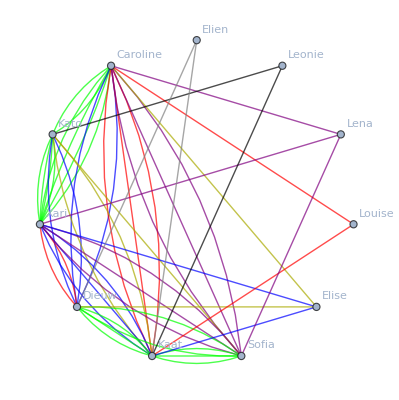

```mathematica
g=Graph[{Caroline,Kato,Xari,Dieuw,Kaat,Sofia,Elise,Louise,Lena, Leonie,Elien},Join[Match1,Match2,Match3, Match4,Match5,Match6,Match7,Match8],
GraphLayout->"CircularEmbedding",
VertexLabels->"Name"
]
```

```mathematica
AdjacencyMatrix[g]//Eigenvalues//N
```

{13.6849,-5.03409,-3.87973,-3.57143,-2.15343,1.10469,-1.01398,0.706875,0.307573,-0.279844,0.128488}

```mathematica
DeleteDuplicates[Map[Sort[{#[[1]],#[[2]]}, BiggerSymbol]&,EdgeList[VertexDelete[g,{Leonie,Lena,Louise}]]]]
```

{{Caroline,Kato},{Caroline,Xari},{Dieuw,Kaat},{Dieuw,Sofia},{Kaat,Sofia},{Kato,Xari},{Caroline,Kaat},{Dieuw,Kato},{Xari,Kato},{Xari,Dieuw},{Xari,Elise},{Xari,Kaat},{Kaat,Elise},{Caroline,Dieuw},{Kato,Dieuw},{Kaat,Kato},{Sofia,Kato},{Caroline,Elise},{Elise,Dieuw},{Caroline,Sofia},{Kaat,Xari},{Xari,Sofia},{Sofia,Xari},{Sofia,Kaat},{Kaat,Dieuw},{Sofia,Caroline},{Elien,Dieuw},{Kaat,Elien}}

```mathematica
BiggerSymbol[s1_,s2_]:=AlphabeticOrder[SymbolName[s1],SymbolName[s2]]==-1
```

```mathematica
BiggerSymbol [Xari,Sofia]
```

True

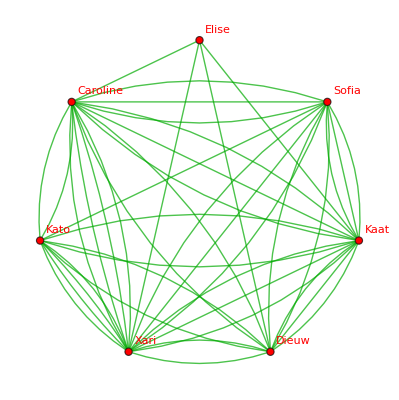

```mathematica
Graph[Map[#[[1]]<->#[[2]]&,EdgeList[VertexDelete[g,{Leonie,Lena,Louise,Elien}]]],VertexLabels->"Name",
GraphLayout->"CircularEmbedding",VertexStyle->Red,EdgeStyle->Darker[Green]]
```

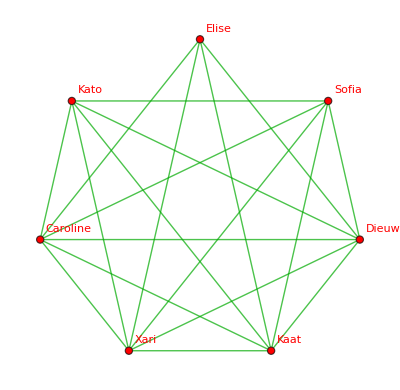

```mathematica
Graph[Map[#[[1]]<->#[[2]]&,DeleteDuplicates[Map[Sort[{#[[1]],#[[2]]}, BiggerSymbol]&,EdgeList[VertexDelete[g,{Leonie,Lena,Louise,Elien}]]]]],VertexLabels->"Name",
GraphLayout->"CircularEmbedding",VertexStyle->Red,EdgeStyle->Darker[Green]]
```

```mathematica
Length[DeleteDuplicates[Sort[Map[Sort[{#[[1]],#[[2]]}]&,EdgeList[VertexDelete [g,Louise]]]]]]
```

26

```mathematica
Sort[Map[Sort[{#[[1]],#[[2]]}]&,EdgeList[GraphComplement[EdgeList[VertexDelete [g,Louise]]]]]]
```

{{Caroline,Elien},{Caroline,Leonie},{Dieuw,Lena},{Dieuw,Leonie},{Elien,Elise},{Elien,Kato},{Elien,Lena},{Elien,Leonie},{Elien,Sofia},{Elien,Xari},{Elise,Kato},{Elise,Lena},{Elise,Leonie},{Elise,Sofia},{Kaat,Lena},{Kato,Lena},{Lena,Leonie},{Leonie,Sofia},{Leonie,Xari}}

```mathematica
EdgeCount[CompleteGraph[7]]
```

21